## First Approach

```mathematica
vert1=Table[{x,Sqrt[3] y},{x,0,20},{y,0,10}];
vert2=Table[{1/2 x,Sqrt[3]/2 y},{x,1,41,2},{y,1,21,2}];
data=RandomReal[{0,20},{500,2}];
```

```mathematica
nearbin=Nearest[Table[verttri[[i]]->i,{i,Length@verttri}]]
counts=BinCounts[nearbin/@data,{1,Length@verttri+1,1}];
With[{maxCount=Max@counts},Graphics[Table[Disk[verttri[[i]],0.5 Sqrt[counts[[i]]/maxCount]],{i,Length@verttri}],Axes->True]]
```

```mathematica
nearbin/@data
```

{{316},{407},{131},{306},{419},{399},{297},{315},{200},{270},{391},{385},{275},{91},{388},{381},{409},{300},{398},{92},{388},{105},{377},{399},{124},{268},{432},{66},{29},{330},{22},{156},{125},{440},{355},{25},{82},{264},{222},{178},{95},{182},{123},{147},{186},{230},{54},{207},{94},{388},{187},{225},{407},{419},{131},{402},{197},{186},{305},{122},{77},{173},{354},{95},{447},{117},{356},{46},{227},{154},{39},{13},{334},{325},{61},{260},{276},{365},{121},{367},{258},{48},{84},{240},{408},{164},{117},{86},{326},{403},{429},{42},{156},{365},{316},{11},{135},{419},{104},{297},{314},{410},{109},{184},{67},{22},{404},{66},{135},{68},{393},{408},{106},{54},{384},{341},{307},{148},{248},{110},{414},{434},{271},{440},{12},{37},{40},{363},{94},{261},{91},{25},{124},{264},{441},{407},{31},{13},{82},{161},{220},{367},{13},{178},{126},{425},{419},{239},{224},{24},{48},{181},{198},{356},{103},{22},{408},{306},{280},{176},{26},{151},{253},{330},{345},{434},{149},{223},{170},{141},{235},{288},{256},{404},{306},{306},{371},{428},{64},{276},{355},{327},{426},{136},{332},{84},{331},{176},{356},{319},{451},{130},{442},{136},{374},{341},{43},{382},{327},{281},{309},{44},{356},{118},{179},{201},{12},{324},{295},{158},{182},{14},{228},{294},{306},{340},{15},{248},{445},{27},{369},{273},{400},{180},{329},{102},{209},{329},{254},{35},{49},{430},{97},{32},{33},{352},{23},{439},{342},{68},{69},{399},{346},{233},{297},{382},{155},{27},{247},{202},{328},{293},{271},{432},{215},{18},{155},{94},{280},{364},{254},{258},{322},{444},{196},{419},{223},{356},{96},{256},{316},{308},{392},{114},{223},{347},{387},{167},{127},{405},{250},{145},{25},{193},{208},{313},{217},{123},{160},{41},{256},{194},{392},{350},{413},{444},{289},{172},{234},{203},{252},{346},{370},{335},{10},{151},{87},{429},{291},{350},{14},{57},{261},{241},{344},{288},{443},{236},{113},{385},{69},{440},{284},{366},{300},{363},{319},{365},{97},{163},{13},{103},{190},{190},{280},{120},{364},{268},{396},{17},{182},{65},{256},{178},{206},{137},{314},{79},{347},{400},{28},{153},{66},{263},{147},{70},{118},{386},{209},{367},{43},{23},{199},{322},{198},{97},{423},{432},{273},{96},{366},{444},{208},{218},{275},{423},{309},{113},{421},{200},{77},{247},{188},{352},{93},{372},{316},{219},{193},{101},{142},{347},{429},{22},{114},{321},{316},{378},{333},{26},{404},{57},{237},{285},{318},{413},{213},{168},{399},{319},{202},{420},{438},{324},{297},{136},{320},{341},{262},{74},{22},{431},{206},{201},{449},{52},{342},{8},{254},{180},{356},{343},{35},{39},{119},{445},{418},{90},{176},{374},{382},{411},{19},{221},{61},{436},{82},{352},{75},{152},{23},{130},{215},{12},{394},{271},{297},{235},{438},{195},{114},{285},{182},{433},{396},{307},{407},{327},{390},{44},{363},{451},{439},{245},{323},{44},{171},{37},{186},{72},{109},{319},{80},{110},{326},{331},{52},{411},{263},{71},{409},{376},{421},{387},{324},{6},{430},{199},{87},{263}}

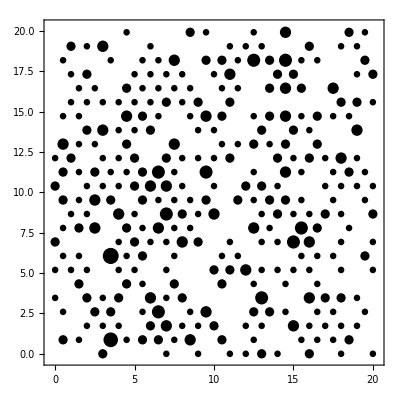

```mathematica
tileContaining[{x_,y_}]:={Floor[x],Sqrt[3] Floor[y/Sqrt[3]]};
nearestWithinTile=Nearest[{{0,0},{1,0},{1/2,Sqrt[3]/2},{0,Sqrt[3]},{1,Sqrt[3]}}];
nearest[point_]:=Module[{tile,relative},
tile=tileContaining[point];
relative=point-tile;
tile+First@nearestWithinTile[relative]];
tally=Tally[nearest/@data];
With[{maxTally=Max[Last/@tally]},Graphics[Disk[#[[1]],1/2 Sqrt[#[[2]]/maxTally]]&/@tally,Axes->True,Frame->True,AxesOrigin->{0,0}]]
```

## Second Approach

```mathematica
<<Polytopes`
f[data_,cs_,ptype_]:=Module[{hc,vh,nearbin,counts,trr,maxCount},hc=Flatten[Table[{i,j},(*hexagons positions*){p,0,1},{j,3 p/2 cs+Min[data[[All,2]]],Max[data[[All,2]]],3 cs},{i,p Sqrt[3]/2 cs+Min[data[[All,1]]],Max[data[[All,1]]],Sqrt[3] cs}],2];
vh=cs Vertices[Hexagon];
nearbin=Nearest[Table[hc[[i]]->i,{i,Length@hc}]];
counts=BinCounts[nearbin/@data,{1,Length@hc+1,1}];
trr[v_,tr_]:=Translate[Rotate[Polygon[v],Pi/2],tr];
maxCount=Max@counts;
Graphics[Table[Switch[ptype,1,{Opacity[counts[[n]]/maxCount],trr[vh,hc[[n]]]},2,trr[counts[[n]]/maxCount vh,hc[[n]]],3,trr[Sqrt[counts[[n]]/maxCount] vh,hc[[n]]]],{n,Length@hc}],Axes->True]]
```

SetDelayed::write: Tag Area in Area[polygon_] is Protected.

```mathematica
cs=1/2;(*cell size*)data=RandomVariate[MultinormalDistribution[{10,10},7 IdentityMatrix[2]],500];
Table[f[data,cs,i],{i,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

## Third Approach

```mathematica
Needs["Polytopes`"];
honeybin[data_,cs_,ptype_,{{xmin_,xmax_},{ymin_,ymax_}}]:=(*"cs_" is the width of a bin,i.e.the distance between bin centers*)Module[{tileContaining,nearestWithinTile,nearest,tally,vh,hexr,trr},tileContaining[{x_,y_}]:={Floor[x],Sqrt[3] Floor[y/Sqrt[3]]};
nearestWithinTile=Nearest[{{0,0},{1,0},{1/2,Sqrt[3]/2},{0,Sqrt[3]},{1,Sqrt[3]}}];
nearest[point_]:=Module[{tile,relative},tile=tileContaining[point];
relative=point-tile;
tile+First@nearestWithinTile[relative]];
vh=cs  Vertices[Hexagon]/Sqrt[3];
trr[v_,tr_]:=Translate[Rotate[Polygon[v],Pi/2],tr];
tally=Tally[cs (nearest/@(data/cs))];
With[{maxTally=Max[Last/@tally]},Graphics[Table[Switch[ptype,1,{Blend[{Lighter[Red,0.99],Darker[Red,0.6]},Sqrt[Last@tally[[n]]/maxTally]],trr[vh,First@tally[[n]]]},2,trr[Last@tally[[n]]/maxTally vh,First@tally[[n]]],3,trr[Sqrt[Last@tally[[n]]/maxTally] vh,First@tally[[n]]]],{n,Length@tally}],Frame->True,PlotRange->{{xmin,xmax},{ymin,ymax}},PlotRangeClipping->True]]]
```

```mathematica
data=RandomVariate[MultinormalDistribution[{10,10},7 IdentityMatrix[2]],100];
honeybin[data,2,1,{{1,15},{3,20}}]
```

-Graphics-

```mathematica
<<Polytopes`
Honeybin[data_,cs_,ptype_,{{xmin_,xmax_},{ymin_,ymax_}}]:=(*"cs_" is the width of a bin,i.e.the distance between bin centers*)Module[{tileContaining,nearestWithinTile,nearest,tally,vh,hexr,trr},
tileContaining[{x_,y_}]:={Floor[x],Sqrt[3] Floor[y/Sqrt[3]]};
nearestWithinTile=Nearest[{{0,0},{1,0},{1/2,Sqrt[3]/2},{0,Sqrt[3]},{1,Sqrt[3]}}];
nearest[point_]:=Module[{tile,relative},
tile=tileContaining[point];
relative=point-tile;
tile+First@nearestWithinTile[relative]];
vh=cs  Vertices[Hexagon]/Sqrt[3];
trr[v_,tr_]:=Translate[Rotate[Polygon[v],Pi/2],tr];
tally=Tally[cs (nearest/@(data/cs))];
Print[tally];
With[{maxTally=Max[Last/@tally]},
Graphics[
Table[
Switch[ptype,1,{Blend[{Lighter[Red,0.99],Darker[Red,0.6]},Sqrt[Last@tally[[n]]/maxTally]],trr[vh,First@tally[[n]]]},
2,trr[Last@tally[[n]]/maxTally vh,First@tally[[n]]],
3,trr[Sqrt[Last@tally[[n]]/maxTally] vh,First@tally[[n]]]
],
{n,Length@tally}
],
Frame->True,
PlotRange->{{xmin,xmax},{ymin,ymax}},
PlotRangeClipping->True]
]
]
data=RandomVariate[MultinormalDistribution[{10,10},7 IdentityMatrix[2]],100];
Honeybin[data,2,1,{{1,15},{3,20}}]
```

SetDelayed::write: Tag Area in Area[polygon_] is Protected.

-Graphics-

```mathematica
Blend[{Lighter[Red,0.99],Darker[Red,0.6]},10]
```

RGBColor[0.4, 0., 0.]